```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[StringDrop[NotebookDirectory[],-4]]
```

H:\2_Projects\physics\5d_flavourful_axion

```mathematica
<<"WarpFlavourAxion`"
```

### Import Data

```mathematica
quarkData = <<"output/yukawa_quark.m";
Print["Number of Yu Yd 3x3 matrix pairs"]
Dimensions[quarkData]
```

Number of Yu Yd 3x3 matrix pairs

{1321,2,3,3}

```mathematica
leptonData = <<"output/yukawa_lepton.m";
Print["Number of Yn Ye 3x3 matrix pairs (normal hierarchy)"]
Dimensions[leptonData[[1]]]
Print["Number of Yn Ye 3x3 matrix pairs (inverted hierarchy)"]
Dimensions[leptonData[[2]]]
```

Number of Yn Ye 3x3 matrix pairs (normal hierarchy)

{4330,2,3,3}

Number of Yn Ye 3x3 matrix pairs (inverted hierarchy)

{}

```mathematica
colorsStandard = ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
colors=
{
{colorsStandard[[5]],colorsStandard[[2]],colorsStandard[[1]]},
{colorsStandard[[2]],colorsStandard[[5]],colorsStandard[[3]]},
{colorsStandard[[1]],colorsStandard[[3]],colorsStandard[[5]]}
}
```

{{RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798]},{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.560181, 0.691569, 0.194885]},{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.528488, 0.470624, 0.701351]}}

```mathematica
getAbs[data_,entry_]:=
GraphicsGrid[
Table[
Histogram[Table[data[[mat,entry]][[i,j]],{mat,1,Length[data]}]//Abs//Threshold,
11,"PDF",Frame->True,PlotRange->{{Automatic,3.02},{0,0.55}},ChartStyle->Directive[colors[[i,j]],Opacity[0.5]]],
{i,1,3},{j,1,3}]
]
```

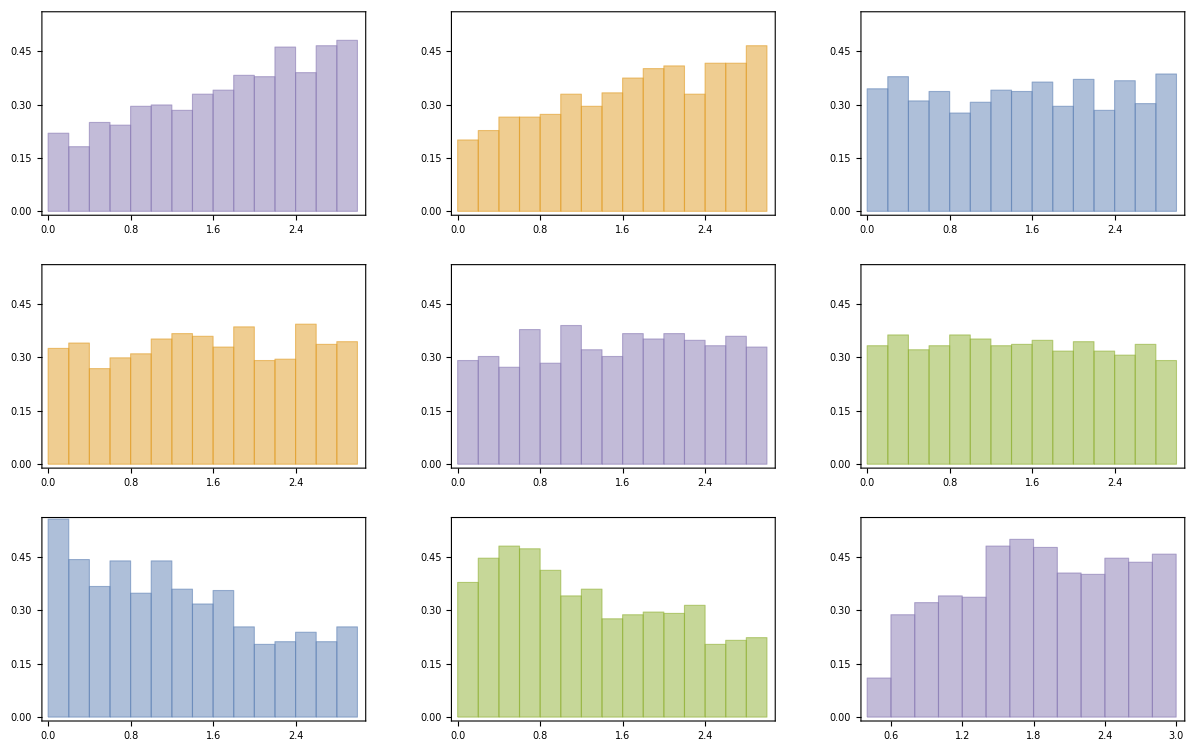

```mathematica
quark = getAbs[quarkData,1]
```

```mathematica
Export["Figures/hist_yukawa_quark.pdf",quark]
```

Figures/hist_yukawa_quark.pdf